```mathematica
Clear["Global`*"]

Constants ;
μ0=4*π*10^(3); (* [ G·um/A] Vacuum permeability *)
c = 2.99*10^(14); (*[um/s] Speed of light*)
h =6.62606957*10^(-34); (*[Js] Planck's constant*)
hbar=h/(2*π);(*[Js] Planck's constant*)
e = 1.60217*10^(-19); (*[C] electron charge*)
ϵ0= 8.854187817*10^(-12); (*[F/m]*)
μB=9.27400915*10^(-28); (* [ J/G] Bohr Magneton *)
kB=1.38064852*10^(-23);(* [ J/K] Bohr Magneton *)
g=9.80665;(*[m/s^2]*) 



Experimental parameters  ;
m=1.443160648*10^(-25); (*[kg] Rb atomic mass*)
ω0=2*Pi*384.2304844685*10^(12); (*[Hz]*)
Γ=2*Pi*6.0666*10^(6); (*[Hz]*)

λ=1064*10^(-3);(*[micron] ODT laser wavelength*) 
ω=(2*π*c)/λ; (*[Hz]*)

CC =(3*π*c*c/(2*(ω0^3)))*((Γ/(ω0-ω))+(Γ/(ω0+ω)));
SC=(3*π*c*c/(2*hbar*(ω0^3)))*(ω/ω0)^3*((Γ/(ω0-ω))+(Γ/(ω0+ω)))^2;

Bgrad=20*10^(-4); (*[G/um] Magnetic field gradient in the weak axis*)
z0=0;(*[um]*)



Parameters Crossed beam @ any angle;
(*y.. direction of gravity Haxial direction of vertical beamL
x.. horizontal,perpendicular to horizontal beam
z.. axial direction of horizontal beam*)
(*Horizontal beam*)
waist1x=50;waist1y=75;P1=1;
(*Vertical beam*)
waist2x=70;waist2z=110;P2=1;
(*Angles between vertical and horizontal beam;alpha rotation in y-z-plane;
beta rotation in x-z-plane;
Corresponds in our experiment to the angle of the vertical beam to the axis
of gravity*)
alpha=90(*°*);
(*Corresponds in our experiment to the angle of the horizontal beam in the
horizontal planeHhalf angle between viewports=14°*)
beta=90(*°*);
η=2;
```

```mathematica
(*---------------------------------------------------------------------------*)

Magnetic potential;
UB[x_,y_,z_]:=(1/(kB*10^(-6)))*(2*μB*Bgrad*Sqrt[(1*x^2)+(4*y^2)+((z-z0)^2)]);
Plot3D[UB[x,y,0], {x,-200,200},{y,-200,200},ColorFunctionScaling->True,ColorFunction->"TemperatureMap",PlotTheme->"Scientific",Mesh->None];
(*--------------------------------------------------------------------------*)
```

```mathematica
Gravity potential;
Ug[x_,y_,z_]:=(1/(kB*10^(-6)))*(m*g*y*10^(-6));
```

```mathematica
(*---------------------------------------------------------------------------*)
```

```mathematica
ODT crossed trap @ any angle;

w[w0_,z_]:=w0*Sqrt[1+(z/zR[w0])^2];
zR[w0_]:=(π*w0*w0)/λ;
zRell[wx_,wy_]:=(zR[wx]*zR[wy])*((zR[wx]^2+zR[wy]^2))^(-1/2);
intensity[P_,w0x_,w0y_,x_,y_,z_]:=(2*P)/(π*w[w0x,z]*w[w0x,z])*Exp[-2*((x^2/w[w0x,z]^2)+(y^2/w[w0y,z]^2))];

wαangle[wz_,wx_,α_,η_]:=1/Sqrt[(((Cos[α*π/180])^2/w[wz,0]^2)+((Sin[α*π/180])^2/(η*zRell[wz,wx]^2)))];
zRellangle[wz_,wx_,α_,η_]:=1/Sqrt[(((Sin[α*π/180])^2/w[wz,0]^2)+((Cos[α*π/180])^2/(η*zRell[wz,wx]^2)))];
w2zβangle[wz_,wx_,β_,α_,η_]:=1/Sqrt[(((Cos[β*π/180])^2/wαangle[wz,wx,α,η]^2)+((Sin[β*π/180])^2/w[wx,0]^2))];
w2xβangle[wz_,wx_,β_,α_,η_]:=1/Sqrt[(((Sin[β*π/180])^2/wαangle[wz,wx,α,η]^2)+((Cos[β*π/180])^2/w[wx,0]^2))];

(*Rotation on the x and z angles*)
xangle[x_,z_]:=(x*Cos[beta*π/180])+(z*Sin[beta*π/180]);
yangle[x_,y_,z_]:=(x*Sin[alpha*π/180]*Sin[beta*π/180])+(y*Cos[alpha*π/180])+(z*Sin[alpha*π/180]*Sin[beta*π/180]);
zangle[x_,y_,z_]:=(-x*Cos[alpha*π/180]*Sin[beta*π/180])+(y*Sin[alpha*π/180])+(z*Cos[alpha*π/180]*Cos[beta*π/180]);

(*New beam waists including angles*)
w2znew=N[w2zβangle[waist2z,waist2x,beta, alpha, 2]];
w2xnew=N[w2xβangle[waist2z,waist2x,beta, alpha, 2]];
zRell2new=N[zRellangle[waist2z,waist2x,alpha,2]];

(*Potential for each beam*)
Uell1[x_,y_,z_]:=(1/(kB*10^(-6)))*(CC*intensity[P1,waist1x,waist1y,x,y,z]);
Uell2[x_,y_,z_]:=(1/(kB*10^(-6)))*(CC*intensity[P2,waist2x,waist2z,xangle[x,z],zangle[x,y,z],yangle[x,y,z]]);
Ucross[x_,y_,z_]:=-Uell1[x,y,z]-Uell2[x,y,z]


(*Total potential*)
U[x_,y_,z_]:=UB[x,y,z]-Uell1[x,y,z]-Uell2[x,y,z]+Ug[x,y,z]; (*[uK]*)


Plot3D[U[x,y,0], {x,-200,200},{y,-200,200},ColorFunctionScaling->True,ColorFunction->"TemperatureMap",PlotTheme->"Scientific",Mesh->None,AxesLabel->{"x(µm)","y(µm)","Udip(µK)"}]
Plot3D[U[x,0,z], {x,-200,200},{z,-200,200},ColorFunctionScaling->True,ColorFunction->"TemperatureMap",PlotTheme->"Scientific",Mesh->None,AxesLabel->{"x(µm)","z(µm)","Udip(µK)"}]
Plot3D[U[0,y,z], {y,-200,200},{z,-200,200},ColorFunctionScaling->True,ColorFunction->"TemperatureMap",PlotTheme->"Scientific",Mesh->None,AxesLabel->{"y(µm)","z(µm)","Udip(µK)"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

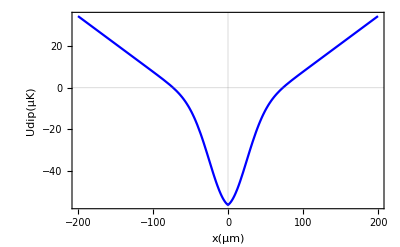

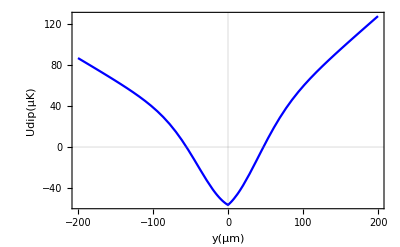

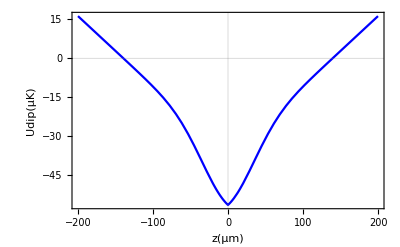

```mathematica
Plot[U[x,0,0], {x,-200,200},PlotTheme->"Scientific",PlotStyle->Blue,AxesLabel->{"x(µm)","Udip(µK)"}]
Plot[U[0,y,0], {y,-200,200},PlotTheme->"Scientific",PlotStyle->Blue,AxesLabel->{"y(µm)","Udip(µK)"}]

Plot[U[0,0,z], {z,-200,200},PlotTheme->"Scientific",PlotStyle->Blue,AxesLabel->{"z(µm)","Udip(µK)"}]
```

```mathematica
Trap depth_horizontal [μK]
U0h=Uell1[0,0,0]
(*[uK] Trap depth*)

Trap depth_vertical [μK]
U0v=Uell2[0,0,0]

Trap freq_x_horizontal [ kHz ]
ωx=(1/(2000*π))*Sqrt[(4/m)*(Uell1[0,0,0]*(kB*10^(-6))/(waist1x*10^(-6))^2)+(((Uell2[0,0,0]*(kB*10^(-6)))/(w2xnew*10^(-6))^2))](*[Hz] Trap freq in x *)
Trap freq_y_vertical [ kHz ]
ωy= (1/(2000*π))*Sqrt[(4/m)*(Uell1[0,0,0]*(kB*10^(-6))/(waist1y*10^(-6))^2)+(((Uell2[0,0,0]*(kB*10^(-6)))/(zRell2new*10^(-6))^2))](*[Hz] Trap freq in x (=ωy)*)

Trap freq_z _axial[kHz ]

ωz= (1/(2000*π))*Sqrt[(1/m)*(2*Uell1[0,0,0]*(kB*10^(-6))/(zRell[waist1x*10^(-6),waist1y*10^(-6)])^2)+(((4*Uell2[0,0,0]*(kB*10^(-6)))/(w2znew*10^(-6))^2))](*[Hz] Trap freq in z *)

(*Scattering rate_horizontal;

Γsc=SC*intensity[P1,waist1x,waist1y,x,y,z];

Scattering rate_vertical;

Γsc=SC*intensity[P2,waist2x,waist2z,xangle[0,0],zangle[0,0,0],yangle[0,0,0]];*)
```

Trap depth_horizontal[μK]

37.4944

Trap depth_vertical[μK]

19.1298

Trap freq_x _horizontal[kHz]

0.381283

Trap freq_y _vertical[kHz]

0.254189

Trap freq_z _axial[kHz]

1998.47